# Filtering Checks - Trend Rule and Targeting

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Independent Components*)
(*independent components-- these are the sensed species set*)
FCL={20,10,5};
CIAL={80,70,68};
F2L={200,30,20};
F3L={3400,420,60};
FML={100,200,50};
FSL={500,150,300};
MPL={50,8500,20};
O2L={1.0,0.481333,1.22222};
kciaL ={0.53328,0.42,1.13322};
kvacL ={2.9997,0.3375,0.16665};
kmitL = {0.541613,6.6375,0.770756};
k23L={0.226644,0.0644,0.0219978};
kcytL ={2.62995,3.10625,4.73869};
kO2L = {91.8291,17.9801,60.7431};
kmpL={0.0016665,0.176593,0.0010908};


filter={};
(*Some helper functions*)
at[list_, index_]:= list[[index]]
nestedAt[list_,row_,col_]:=at[at[list,row],col]
```

Initially, we have quite a lot of cases to consider!

```mathematica
components = {FCL, CIAL, F2L, F3L, FML, FSL, MPL, O2L};
combos = Tuples[components, 7];
Length[combos]
```

2097152

However, not all these combinations are valid. For example, a component can be a potential candidate for regulating a rate constant if the rate constant and component trend in the same direction (e.g. perfect positive or negative correlation).

```mathematica
(*Define the trend rule*)
areValidPoints[data_]:=If[nestedAt[data,1,2]>nestedAt[data,2,2]>nestedAt[data,3,2]||nestedAt[data,1,2]<nestedAt[data,2,2]<nestedAt[data,3,2],True,False]
isDecreasing[data_]:=nestedAt[data,1,2]>nestedAt[data,2,2]>nestedAt[data,3,2]
isIncreasing[data_]:=nestedAt[data,1,2]<nestedAt[data,2,2]<nestedAt[data,3,2]
```

```mathematica
generateData[X_,Y_]:={{at[X,1],at[Y,1]},{at[X,2],at[Y,2]},{at[X,3],at[Y,3]}}
(*Apply the trend rule to all the combinations*)
kvalues = {k23L, kciaL, kvacL, kmitL, kcytL, kO2L,kmpL};
STOP = Length[combos];
filter={};
For[i=1, i<= STOP, i+=1, 
entry = at[combos, i];
truthvalues = {};
For[j = 1, j<= 7, j+=1,
X = at[entry,j];
Y = at[kvalues,j]; 
sorted = Sort[generateData[X,Y]];
AppendTo[truthvalues, areValidPoints[sorted]];
];
If[AllTrue[truthvalues, TrueQ], AppendTo[filter, entry], "not valid"];
]
Length[filter]
```

576

Note that our initial set of regulatory combinations to look for was quite small -- just around 2.1 million. Thus, we were able to do a complete search over all combinations to see which combinations followed the trend rule. Applying the trend rule eliminated over 99% of combinations -- now we can focus on these cases. 
First, let us define the regulatory functions we got from nonlinear regression.

```mathematica
RegFunction[k_, n_, SP_, C_, x_]:=k/(1+Exp[n*(x-SP)])+C
getk23[list_]:=Module[{fccase,ciacase,f2case,f3case},fccase=RegFunction[0.293708,-0.248768,15.105,0,FC[t]];
ciacase=RegFunction[0.227484,-0.652642,71.4237,0,CIA[t]];
f2case=RegFunction[0.226644,-0.130635,37.073,0,F2[t]];
f3case=RegFunction[0.226655,-0.00362872,674.652,0,F3[t]];
Switch[list,FCL,fccase,CIAL,ciacase,F2L,f2case,F3L,f3case]]
getkO2[list_]:=Module[{fscase},fscase=RegFunction[95.3616,-0.0134783,258.284,0,FS[t]];
Switch[list,FSL,fscase]]
getkCIA[list_]:=Module[{o2case,fmcase,mpcase},o2case=RegFunction[4.661,-8.87757,1.41475,0.418826,O2[t]];
fmcase=RegFunction[5.50768,0.0387998,0.991932,0.41756,FM[t]];
mpcase=RegFunction[3.006,0.0690787,3.09565,0.42,MP[t]];
Switch[list,O2L,o2case,FML,fmcase,MPL,mpcase]]
getkCYT[list_]:=Module[{f2case,ciacase,f3case,fccase},f2case=RegFunction[16.6101,0.159447,7.90727,2.62995,F2[t]];
ciacase=RegFunction[1557.4,0.744197,59.1271,2.62967,CIA[t]];
f3case=RegFunction[5.00448,0.00537466,0.991933,2.62995,F3[t]];
fccase=RegFunction[2.15854,1.00162,8.74028,2.62992,FC[t]];
Switch[list,F2L,f2case,CIAL,ciacase,F3L,f3case,FCL,fccase]]
getkMIT[list_]:=Module[{fscase},fscase=RegFunction[168.632,0.022031,0.991933,0.538779,FS[t]];
Switch[list,FSL,fscase]]
getkMP[list_]:=Module[{o2case,mpcase,fmcase},o2case=RegFunction[4.1828,8.89003,0.130172,0,O2[t]];
mpcase=RegFunction[0.176593,-0.0142367,376.877,0,MP[t]];
fmcase=RegFunction[0.931282,-0.0587368,224.854,0.00105854,FM[t]];
Switch[list,O2L,o2case,MPL,mpcase,FML,fmcase]]
getkVAC[list_]:=Module[{f2case,ciacase,f3case,fccase},f2case=RegFunction[2.99975,-0.076787,56.8973,0,F2[t]];
ciacase=RegFunction[3.67913,-0.377767,76.0689,0,CIA[t]];
f3case=RegFunction[3.04175,-0.00213037,1396.83,0,F3[t]];
fccase=RegFunction[2.88787,-0.679725,14.0134,0.160357,FC[t]];
Switch[list,F2L,f2case,CIAL,ciacase,F3L,f3case,FCL,fccase]]


getSensed[list_]:= Switch[list, FCL, "FCL",  CIAL, "CIAL",  F2L, "F2L",  F3L, "F3L",  FML, "FML",  FSL,"FSL",  MPL,"MPL",  O2L, "O2L" ]
```

Once we have a case we want to inspect, we will only check to make sure that the case’s regulatory system (set of logistic functions) can accurately predict the three given states within a reasonable error. Thus, we should create a function that allows us to just check only the outputted steady state values for a particular transition. In this we are only looking for three major transitions: W → W, W → Y,  and W → D.

One key idea to note is that α, or the growth rate of the cell is linked to kisu. This is because kisu remains constant for both the wild type and iron deficient states, but only changes for the Yfh1 state. Thus, it cannot be regulated based on the trend rule. But since it changes we can treat the relationship between kisu (independent) and α (dependent) as a linear relation.

We can discard a case if its maximum percent error for any component between its expected (no regulation) and its predicted (with regulation) steady state values exceed an arbitrary threshold.

```mathematica
isValidSensed[candidates_, regs_, Fe0_, kisu0_,o2level_, benchmark_,tolerance_]:=
Module[{alpha, IRON, k32, kisu, Kcyt, Kvac, Kcia, Kisu, KresO2, K32, Kmit,OXYGEN, K32NAH, CARBON, kres, k23, kcia, kvac, kmp, kmit, yvals, kcyt, kO2, Rcyt, Rmit, Rvac, Rcia, Risu, Rmp, RO2, Rres, R23, R32, ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, ode9, eqns, s, x,y,z,b,c,d,n,g,k,k0,k1,k2,k3,k4,k5, k6, k7, k8, k9, line,X,Y, data,func, S,species, aggregate, ret, actual, expected, check, i, maxtest,KF2,O2SP,fcyt,fvac,fmit,s0,s1,s2,s3,s4,s5,s6,s7,s8},
IRON =Fe0;

kisu =kisu0; 
(*Linear relation between kisu and alpha*)
alpha = 0.000222188885555*kisu + 0.00185188888889;

Kcyt = 10;
Kmit = 20;
Kvac = 20;
Kcia = 20; 
Kisu = 100;
KresO2 = 1;
KF2 = 200; 
K32 = 800;
O2SP = 1; 
OXYGEN = o2level; 
 CARBON = 100; 
kres =36.363636363636363636364;

k23 = 0;
kcia =0;
kvac = 0;
kmit = 0;
kcyt =0;
kO2 =0;
kmp = 0; 
yvals = { k23, kcia, kvac, kmit,kcyt, kO2,kmp};

aggregate = {};
For[i = 1, i ≤ Length[regs], i+=1,
yvals[[i]] =regs[[i]];
];

k23 = at[regs, 1];
kcia =at[regs, 2];
kvac = at[regs, 3];
kmit = at[regs, 4];
kcyt =at[regs, 5];
kO2 =at[regs, 6];
kmp =at[regs,7];

(*rate constants are reg functions*)
Rcyt = kcyt * IRON/(Kcyt + IRON);
Rmit = kmit * FC[t]/(Kmit + FC[t]);
Rvac = kvac * FC[t]/(Kvac + FC[t]);
Rcia = kcia * FC[t]/(Kcia+FC[t]);
Risu = kisu * FM[t]/(Kisu + FM[t])*O2SP/(O2SP+O2[t]);
Rmp = kmp * FM [t]* O2[t];
RO2 = kO2 * (OXYGEN- O2[t]); 
Rres = kres * FS[t] * O2[t]/(KresO2 + O2[t]);
R23 = k23 * F2[t] /(KF2+F2[t])*OXYGEN;
fcyt=0.8;
fmit=0.1;
fvac=0.1;


ode1=FC'[t]==Rcyt-Rvac-Rmit-Rcia-alpha*FC[t];
ode2=CIA'[t]==Rcia-alpha*CIA[t];
ode3=F2'[t]==fcyt/fvac*Rvac-R23-alpha*F2[t];
ode4=F3'[t]==R23-alpha*F3[t];
ode5=FM'[t]==fcyt/fmit*Rmit-Risu-Rmp-alpha*FM[t];
ode6=FS'[t]==Risu-alpha*FS[t];
ode7=MP'[t]==Rmp-alpha*MP[t];
ode8=O2'[t]==RO2-Rmp-Rres-alpha*O2[t];

eqns = {ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, FC[0] ==20, CIA[0]==80, F2[0] == 200, F3[0]==3400, FM[0]==100,MP[0]== 50, FS[0]==500, O2[0]== 1};
s = NDSolve[eqns,{FC, CIA, F2, F3, FM, FS, MP, O2},{t, 0, 500000}];

<<NumericalCalculus`;

s0 =at[MP[50000]/.s,1];
s1 = at[FC[50000]/.s,1];
s2 =at[F2[50000]/.s,1];
s3 = at[CIA[50000]/.s,1];
s4 =  at[FS[50000]/.s,1];
s5 = at[F3[50000]/.s,1];
s6 =at[O2[50000]/.s,1];
s7 = at[FM[50000]/.s,1];
actual = {s0, s1, s2, s3, s4, s5, s6, s7};

(*Reasonable percent error*)
expected= benchmark;
ret = {};
For[i = 1, i ≤Length[actual], i+=1,
check =Abs[(at[actual, i] -at[expected, i])/at[expected, i]];
ret = Append[ret, check];
];
(**Print[Max[ret]," " ,kisu0," ",Fe0," ",k9];**)
(**If[Max[ret] <= 0.8, Print[Max[ret]," " ,kisu0," ",Fe0," ",k9], "invalid"];**)
 If[ Max[ret]≤tolerance, True, False]

]
validCasesFound = 0;
For[i=1, i ≤Length[filter], i+=1,
candidate = at[filter, i];
regs = {0,0,0,0,0,0,0};
sensed = {};

For[j = 1, j ≤ 7, j+=1,
X = at[candidate, j];

SENSED = getSensed[X];

AppendTo[sensed,ToString[SENSED]];
];

regs[[1]] = getk23[at[candidate, 1]];
regs[[2]] = getkCIA[at[candidate, 2]];
regs[[3]] = getkVAC[at[candidate, 3]];
regs[[4]] = getkMIT[at[candidate, 4]];
regs[[5]] = getkCYT[at[candidate, 5]];
regs[[6]] = getkO2[at[candidate, 6]];
regs[[7]] = getkMP[at[candidate,7]];
(**MP, FC, F2, CIA, FS, F3, O2, FM**)

WB = {50, 20, 200, 80, 500, 3400, 1.0, 100};
YB = {8500, 10, 30, 70,150, 420, 0.481333, 200};
DB = {20, 5, 20,68, 300, 60,1.22222, 50};
wstate = isValidSensed[candidate, regs, 40,6.666,100, WB,0.01]; 
If[wstate == False, Continue[],  ""];

ystate = isValidSensed[candidate, regs, 40, 6.666/10,100, YB,0.01];
If[ystate == False, Continue[],  ""];
dstate = isValidSensed[candidate, regs, 1, 6.666,100, DB,0.01];
If[dstate == False, Continue[],  ""];

If[wstate && ystate && dstate, Print[sensed];validCasesFound+=1;, "Not valid"];
];
Print["Total Cases Found: ", validCasesFound];
```

{FCL,FML,FCL,FSL,FCL,FSL,FML}

{FCL,FML,FCL,FSL,FCL,FSL,MPL}

{FCL,FML,FCL,FSL,F2L,FSL,FML}

{FCL,FML,FCL,FSL,F2L,FSL,MPL}

{FCL,FML,FCL,FSL,F3L,FSL,FML}

{FCL,FML,FCL,FSL,F3L,FSL,MPL}

{FCL,FML,CIAL,FSL,FCL,FSL,FML}

{FCL,FML,CIAL,FSL,FCL,FSL,MPL}

{FCL,FML,CIAL,FSL,F3L,FSL,FML}

{FCL,FML,CIAL,FSL,F3L,FSL,MPL}

{FCL,FML,F3L,FSL,F3L,FSL,FML}

{FCL,FML,F3L,FSL,F3L,FSL,MPL}

{FCL,MPL,FCL,FSL,FCL,FSL,FML}

{FCL,MPL,FCL,FSL,FCL,FSL,MPL}

{FCL,MPL,FCL,FSL,CIAL,FSL,FML}

{FCL,MPL,FCL,FSL,F2L,FSL,FML}

{FCL,MPL,FCL,FSL,F2L,FSL,MPL}

{FCL,MPL,FCL,FSL,F3L,FSL,FML}

{FCL,MPL,FCL,FSL,F3L,FSL,MPL}

{FCL,MPL,CIAL,FSL,FCL,FSL,MPL}

{FCL,MPL,CIAL,FSL,F3L,FSL,MPL}

{FCL,MPL,F3L,FSL,F3L,FSL,FML}

{FCL,MPL,F3L,FSL,F3L,FSL,MPL}

{FCL,O2L,FCL,FSL,FCL,FSL,FML}

{FCL,O2L,FCL,FSL,FCL,FSL,MPL}

{FCL,O2L,FCL,FSL,CIAL,FSL,FML}

{FCL,O2L,FCL,FSL,CIAL,FSL,MPL}

{FCL,O2L,FCL,FSL,F2L,FSL,FML}

{FCL,O2L,FCL,FSL,F2L,FSL,MPL}

{FCL,O2L,FCL,FSL,F3L,FSL,FML}

{FCL,O2L,FCL,FSL,F3L,FSL,MPL}

{FCL,O2L,F3L,FSL,F3L,FSL,FML}

{FCL,O2L,F3L,FSL,F3L,FSL,MPL}

{CIAL,FML,FCL,FSL,FCL,FSL,FML}

{CIAL,FML,FCL,FSL,FCL,FSL,MPL}

{CIAL,FML,FCL,FSL,F3L,FSL,FML}

{CIAL,FML,FCL,FSL,F3L,FSL,MPL}

{CIAL,FML,CIAL,FSL,FCL,FSL,FML}

{CIAL,FML,CIAL,FSL,FCL,FSL,MPL}

{CIAL,FML,CIAL,FSL,F3L,FSL,FML}

{CIAL,FML,CIAL,FSL,F3L,FSL,MPL}

{CIAL,FML,F3L,FSL,FCL,FSL,FML}

{CIAL,FML,F3L,FSL,FCL,FSL,MPL}

{CIAL,FML,F3L,FSL,F3L,FSL,FML}

{CIAL,FML,F3L,FSL,F3L,FSL,MPL}

{CIAL,MPL,FCL,FSL,FCL,FSL,FML}

{CIAL,MPL,FCL,FSL,FCL,FSL,MPL}

{CIAL,MPL,FCL,FSL,CIAL,FSL,FML}

{CIAL,MPL,FCL,FSL,F3L,FSL,FML}

{CIAL,MPL,FCL,FSL,F3L,FSL,MPL}

{CIAL,MPL,CIAL,FSL,FCL,FSL,MPL}

{CIAL,MPL,CIAL,FSL,F3L,FSL,MPL}

{CIAL,MPL,F3L,FSL,FCL,FSL,FML}

{CIAL,MPL,F3L,FSL,FCL,FSL,MPL}

{CIAL,MPL,F3L,FSL,F3L,FSL,FML}

{CIAL,MPL,F3L,FSL,F3L,FSL,MPL}

{CIAL,O2L,FCL,FSL,FCL,FSL,FML}

{CIAL,O2L,FCL,FSL,FCL,FSL,MPL}

{CIAL,O2L,FCL,FSL,CIAL,FSL,FML}

{CIAL,O2L,FCL,FSL,CIAL,FSL,MPL}

{CIAL,O2L,FCL,FSL,F3L,FSL,FML}

{CIAL,O2L,FCL,FSL,F3L,FSL,MPL}

{CIAL,O2L,F3L,FSL,FCL,FSL,FML}

{CIAL,O2L,F3L,FSL,FCL,FSL,MPL}

{CIAL,O2L,F3L,FSL,F3L,FSL,FML}

{CIAL,O2L,F3L,FSL,F3L,FSL,MPL}

{F2L,FML,FCL,FSL,FCL,FSL,FML}

{F2L,FML,FCL,FSL,FCL,FSL,MPL}

{F2L,FML,FCL,FSL,F2L,FSL,FML}

{F2L,FML,FCL,FSL,F2L,FSL,MPL}

{F2L,FML,FCL,FSL,F3L,FSL,FML}

{F2L,FML,FCL,FSL,F3L,FSL,MPL}

{F2L,FML,CIAL,FSL,FCL,FSL,FML}

{F2L,FML,CIAL,FSL,FCL,FSL,MPL}

{F2L,FML,CIAL,FSL,F2L,FSL,FML}

{F2L,FML,CIAL,FSL,F2L,FSL,MPL}

{F2L,FML,CIAL,FSL,F3L,FSL,FML}

{F2L,FML,CIAL,FSL,F3L,FSL,MPL}

{F2L,FML,F2L,FSL,FCL,FSL,FML}

{F2L,FML,F2L,FSL,FCL,FSL,MPL}

{F2L,FML,F2L,FSL,F2L,FSL,FML}

{F2L,FML,F2L,FSL,F2L,FSL,MPL}

{F2L,FML,F2L,FSL,F3L,FSL,FML}

{F2L,FML,F2L,FSL,F3L,FSL,MPL}

{F2L,FML,F3L,FSL,F2L,FSL,MPL}

{F2L,FML,F3L,FSL,F3L,FSL,MPL}

{F2L,MPL,FCL,FSL,FCL,FSL,FML}

{F2L,MPL,FCL,FSL,FCL,FSL,MPL}

{F2L,MPL,FCL,FSL,CIAL,FSL,FML}

{F2L,MPL,FCL,FSL,F2L,FSL,FML}

{F2L,MPL,FCL,FSL,F2L,FSL,MPL}

{F2L,MPL,FCL,FSL,F3L,FSL,FML}

{F2L,MPL,FCL,FSL,F3L,FSL,MPL}

{F2L,MPL,CIAL,FSL,FCL,FSL,MPL}

{F2L,MPL,CIAL,FSL,F3L,FSL,MPL}

{F2L,MPL,F2L,FSL,FCL,FSL,FML}

{F2L,MPL,F2L,FSL,FCL,FSL,MPL}

{F2L,MPL,F2L,FSL,CIAL,FSL,FML}

{F2L,MPL,F2L,FSL,F2L,FSL,FML}

{F2L,MPL,F2L,FSL,F2L,FSL,MPL}

{F2L,MPL,F2L,FSL,F3L,FSL,FML}

{F2L,MPL,F2L,FSL,F3L,FSL,MPL}

{F2L,MPL,F3L,FSL,F2L,FSL,MPL}

{F2L,MPL,F3L,FSL,F3L,FSL,MPL}

{F2L,O2L,FCL,FSL,FCL,FSL,FML}

{F2L,O2L,FCL,FSL,FCL,FSL,MPL}

{F2L,O2L,FCL,FSL,CIAL,FSL,FML}

{F2L,O2L,FCL,FSL,CIAL,FSL,MPL}

{F2L,O2L,FCL,FSL,F2L,FSL,FML}

{F2L,O2L,FCL,FSL,F2L,FSL,MPL}

{F2L,O2L,FCL,FSL,F3L,FSL,FML}

{F2L,O2L,FCL,FSL,F3L,FSL,MPL}

{F2L,O2L,F2L,FSL,FCL,FSL,FML}

{F2L,O2L,F2L,FSL,FCL,FSL,MPL}

{F2L,O2L,F2L,FSL,CIAL,FSL,FML}

{F2L,O2L,F2L,FSL,CIAL,FSL,MPL}

{F2L,O2L,F2L,FSL,F2L,FSL,FML}

{F2L,O2L,F2L,FSL,F2L,FSL,MPL}

{F2L,O2L,F2L,FSL,F3L,FSL,FML}

{F2L,O2L,F2L,FSL,F3L,FSL,MPL}

{F2L,O2L,F3L,FSL,F2L,FSL,MPL}

{F2L,O2L,F3L,FSL,F3L,FSL,MPL}

{F3L,FML,FCL,FSL,FCL,FSL,FML}

{F3L,FML,FCL,FSL,FCL,FSL,MPL}

{F3L,FML,FCL,FSL,F3L,FSL,FML}

{F3L,FML,FCL,FSL,F3L,FSL,MPL}

{F3L,FML,CIAL,FSL,FCL,FSL,FML}

{F3L,FML,CIAL,FSL,FCL,FSL,MPL}

{F3L,FML,CIAL,FSL,F3L,FSL,FML}

{F3L,FML,CIAL,FSL,F3L,FSL,MPL}

{F3L,FML,F3L,FSL,F3L,FSL,MPL}

{F3L,MPL,FCL,FSL,FCL,FSL,FML}

{F3L,MPL,FCL,FSL,FCL,FSL,MPL}

{F3L,MPL,FCL,FSL,CIAL,FSL,FML}

{F3L,MPL,FCL,FSL,F3L,FSL,FML}

{F3L,MPL,FCL,FSL,F3L,FSL,MPL}

{F3L,MPL,CIAL,FSL,FCL,FSL,MPL}

{F3L,MPL,CIAL,FSL,F3L,FSL,MPL}

{F3L,MPL,F3L,FSL,F3L,FSL,MPL}

{F3L,O2L,FCL,FSL,FCL,FSL,FML}

{F3L,O2L,FCL,FSL,FCL,FSL,MPL}

{F3L,O2L,FCL,FSL,CIAL,FSL,FML}

{F3L,O2L,FCL,FSL,CIAL,FSL,MPL}

{F3L,O2L,FCL,FSL,F3L,FSL,FML}

{F3L,O2L,FCL,FSL,F3L,FSL,MPL}

{F3L,O2L,F3L,FSL,F3L,FSL,MPL}

Total Cases Found: 146

An arbitrary maximum percent error of 0.01 may seem harsh, but if redo this analysis with around an error of 10% (0.1), we do not see a change in accepted cases.

```mathematica
validCasesFound = 0;
foundInvalidCase = False;
For[i=1, i ≤Length[filter], i+=1,
candidate = at[filter, i];
regs = {0,0,0,0,0,0,0};
sensed = {};

For[j = 1, j ≤ 7, j+=1,
X = at[candidate, j];

SENSED = getSensed[X];

AppendTo[sensed,ToString[SENSED]];
];

regs[[1]] = getk23[at[candidate, 1]];
regs[[2]] = getkCIA[at[candidate, 2]];
regs[[3]] = getkVAC[at[candidate, 3]];
regs[[4]] = getkMIT[at[candidate, 4]];
regs[[5]] = getkCYT[at[candidate, 5]];
regs[[6]] = getkO2[at[candidate, 6]];
regs[[7]] = getkMP[at[candidate,7]];
(**MP, FC, F2, CIA, FS, F3, O2, FM**)

WB = {50, 20, 200, 80, 500, 3400, 1.0, 100};
YB = {8500, 10, 30, 70,150, 420, 0.481333, 200};
DB = {20, 5, 20,68, 300, 60,1.22222, 50};
wstate = isValidSensed[candidate, regs, 40,6.666,100, WB,0.1]; 

If[wstate == False,Continue[],  ""];

ystate = isValidSensed[candidate, regs, 40, 6.666/10,100, YB,0.1];
If[ystate == False, Continue[],  ""];
dstate = isValidSensed[candidate, regs, 1, 6.666,100, DB,0.1];
If[dstate == False, Continue[],  ""];

If[wstate && ystate && dstate, validCasesFound+=1;, "Not valid"];
];
Print["Total Cases Found with MPE of 10: ", validCasesFound];
```

Total Cases Found with MPE of 10: 146

## Cases that Fail Demo

What does a bad case look like for targeting? Going through the cases, that made the filter, we notice that F2, O2, CIA, FS, F3, FS, and MP do not make it past the targeting. Let us see this failed case for the “transition” between wild type to wild type.

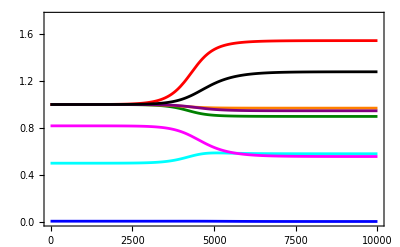

```mathematica
failedRegulation = {0,0,0,0,0,0,0};
failedRegulation[[1]] = getk23[F2L];
failedRegulation[[2]] = getkCIA[O2L];
failedRegulation[[3]] = getkVAC[CIAL];
failedRegulation[[4]] = getkMIT[FSL];
failedRegulation[[5]] = getkCYT[F3L];
failedRegulation[[6]] = getkO2[FSL];
failedRegulation[[7]] = getkMP[MPL];
simulateTimeTransition[startStateValue_, regs_, startIron_, startkisu_] := Module[{alpha, kisu, Kcyt, Kmit, Kvac, Kcia, Kisu, KresO2, KF2, O2SP, OXYGEN, CARBON, kres, k23, kcia, kvac, caseValue, IRON, kmit, kcyt, kO2, kmp, Rcyt, Rmit, Rvac, Rcia, Risu, Rmp, RO2, Rres, R23, fcyt, fmit, fvac, ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, eqns, s},
caseValue = caseId;
IRON = startIron;
kisu =startkisu; 
alpha = 0.000222188885555*kisu + 0.00185188888889;

Kcyt = 10;
Kmit = 20;
Kvac = 20;
Kcia = 20; 
Kisu = 100;
KresO2 = 1;
KF2 = 200; 
O2SP = 1; 
OXYGEN = 100; 
 CARBON = 100; 
kres =36.363636363636363636364;




k23 = at[regs, 1];
kcia =at[regs, 2];
kvac = at[regs, 3];
kmit = at[regs, 4];
kcyt =at[regs, 5];
kO2 =at[regs, 6];
kmp =at[regs,7];
Rcyt = kcyt * IRON/(Kcyt + IRON);
Rmit = kmit * FC[t]/(Kmit + FC[t]);
Rvac = kvac * FC[t]/(Kvac + FC[t]);
Rcia = kcia * FC[t]/(Kcia+FC[t]);
Risu = kisu * FM[t]/(Kisu + FM[t])*O2SP/(O2SP+O2[t]);
Rmp = kmp * FM [t]* O2[t];
RO2 = kO2 * (OXYGEN- O2[t]); 
Rres = kres * FS[t] * O2[t]/(KresO2 + O2[t]);
R23 = k23 * F2[t] /(KF2+F2[t])*OXYGEN;
fcyt = 0.8;
fmit = 0.1;
fvac = 0.1; 
ode1=FC'[t]==Rcyt-Rvac-Rmit-Rcia-alpha*FC[t];
ode2=CIA'[t]==Rcia-alpha*CIA[t];
ode3=F2'[t]==fcyt/fvac*Rvac-R23-alpha*F2[t];
ode4=F3'[t]==R23-alpha*F3[t];
ode5=FM'[t]==fcyt/fmit*Rmit-Risu-Rmp-alpha*FM[t];
ode6=FS'[t]==Risu-alpha*FS[t];
ode7=MP'[t]==Rmp-alpha*MP[t];
ode8=O2'[t]==RO2-Rmp-Rres-alpha*O2[t];
eqns = {ode1, ode2, ode3, ode4, ode5, ode6, ode7, ode8, FC[0] ==FCL[[startStateValue]], CIA[0]==CIAL[[startStateValue]], F2[0] == F2L[[startStateValue]], F3[0]==F3L[[startStateValue]], FM[0]==FML[[startStateValue]],MP[0]== MPL[[startStateValue]], FS[0]==FSL[[startStateValue]], O2[0]== O2L[[startStateValue]]};
s = NDSolve[eqns,{FC, CIA, F2, F3, FM, FS, MP, O2},{t, 0, 500000}];
<<NumericalCalculus`;
s]

getNormalizedPlot[regs_, startState_, startIron_, startkisu_, maxtime_, linethickness_, maxYValue_]:= Module[{s,a,c,e,d,f,g,h,i},
s = simulateTimeTransition[startState, regs, startIron, startkisu];

a = Plot[Rescale[Evaluate[MP[t]/. s],{0,Max[MPL]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Blue,Thickness[linethickness]}];

c = Plot[Rescale[Evaluate[FC[t]/. s],{0, Max[FCL]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Red,Thickness[linethickness]}];

d = Plot[Rescale[Evaluate[F2[t]/. s],{0, Max[F2L]}], {t,0, maxtime}, PlotRange->{0,30}, PlotStyle->{RGBColor[0,0.5,0],Thickness[linethickness]}];e = Plot[Rescale[Evaluate[CIA[t]/. s],{0,Max[CIAL]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Orange,Thickness[linethickness]}];f = Plot[Rescale[Evaluate[F3[t]/. s],{0, Max[F3L]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Purple,Thickness[linethickness]}];

g = Plot[Rescale[Evaluate[FS[t]/. s],{0, Max[FSL]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Black,Thickness[linethickness]}];
h = Plot[Rescale[Evaluate[FM[t]/. s],{0,Max[FML]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Cyan,Thickness[linethickness]}];
i = Plot[Rescale[Evaluate[O2[t]/. s],{0,Max[O2L]}], {t,0, maxtime}, PlotRange->{0,10}, PlotStyle->{Magenta,Thickness[linethickness]}];

 Show[a,c,d,e,f,g,h,i,PlotRange-> {{0,10000},{0.0, maxYValue}}, BaseStyle->{PrintPrecision->2},Axes->False,Frame->{{True,False},{True,False}} 
]];
failedDemoFigure = getNormalizedPlot[failedRegulation, 1,40,6.666,10000, 0.005, 1.75]
```

We notice that the case seems fine for the first 3000 minutes but near the 4000 minute mark it diverges from the wild type state. In contrast,  CRM 1 does not show any deviation from the same transition.

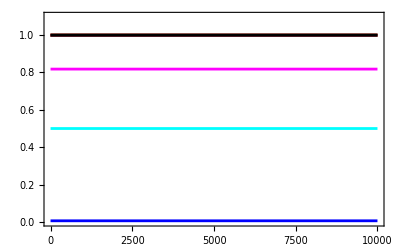

```mathematica
passRegulation = {0,0,0,0,0,0,0};
passRegulation[[1]] = getk23[FCL];
passRegulation[[2]] = getkCIA[FML];
passRegulation[[3]] = getkVAC[FCL];
passRegulation[[4]] = getkMIT[FSL];
passRegulation[[5]] = getkCYT[FCL];
passRegulation[[6]] = getkO2[FSL];
passRegulation[[7]] = getkMP[FML];
passedDemoFigure = getNormalizedPlot[passRegulation, 1,40,6.666,10000, 0.005, 1.1]
```

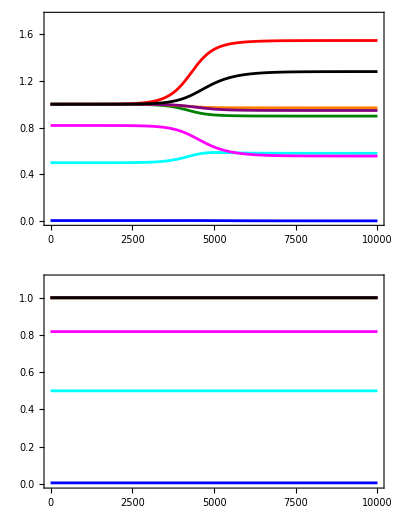
-Graphics-Time (minutes)Normalized Component Concentration

```mathematica
failedandPassingTargetingFigure =Legended[Labeled[GraphicsColumn[{failedDemoFigure, passedDemoFigure}],{"Time (minutes)","Normalized Component Concentration"},{Bottom,Left},RotateLabel->True],LineLegend[{Blue, Red, RGBColor[0,0.5,0], Orange, Purple,  Black ,Cyan, Magenta}, {"MP","FC","F2","CIA","F3","FS","FM","O2"}]]
```

```mathematica
Export["../SavedFigures/failedandPassedTargeting.png",failedandPassingTargetingFigure,ImageResolution-> 500];
```